```mathematica
dictionaryBackward[pairs_,nodes_]:=
Module[{n, new},
n = Length[pairs];
new = For[i=1,i≤n,i++, Sow[Sort[nodes[[pairs[[i]]]]]]]//Reap//Last//Last;
new];
```

```mathematica
deleteduplicatepairs[pairs_]:=
Module[{dups, todelete, temp},
positionDuplicates[list_]:=GatherBy[Range@Length[list],list[[#]]&];
dups = positionDuplicates[Do[Sow[Sort[pairs[[x]]]],{x,Length[pairs]}]//Reap//Last//Last];
temp = For[i=1,i<Length[dups]+1,i++,For[j=2,j<Length[dups[[i]]]+1,j++,Sow[{dups[[i]][[j]]}]]]//Reap//Last;
If[temp === {}, todelete = {}, todelete = temp//Last];
Delete[pairs,todelete]];
```

```mathematica
modifiedEffectiveTransition[G_,k_]:=
Module[{M,spec,R,prediction, n, range,nodes,positions,cutoff},
nodes = VertexList[G];
n = VertexCount[G];
range = Range[n];
M=N[AdjacencyMatrix[G]];
spec=Max[Abs[Eigenvalues[M,1]]];
R=RandomReal[{0,1},{n,n}];
For[i=1,i≤n,i++,For[j=i+1,j≤n,j++,R[[i]][[j]]=(M[[{i,j},{i,j}]]-M[[{i,j},Complement[range,{i,j}]]].Inverse[M[[Complement[range,{i,j}],Complement[range,{i,j}]]]-spec*IdentityMatrix[n-2]].M[[Complement[range,{i,j}],{i,j}]])[[1]][[2]] ]]
For[i=2,i≤n,i++,
For[j=1,j≤i-1,j++, R[[i]][[j]]=(M[[{i,j},{i,j}]]-M[[{i,j},Complement[range,{i,j}]]].Inverse[M[[Complement[range,{i,j}],Complement[range,{i,j}]]]-spec*IdentityMatrix[n-2]].M[[Complement[range,{i,j}],{i,j}]])[[1]][[2]] ]]
For[i=1,i≤n,i++,
R[[i]][[i]]=0;];
cutoff = TakeLargest[Flatten[R-10M],2*k][[2*k]];
positions = deleteduplicatepairs[Position[R-10M,_?(#≥ cutoff&)]];
dictionaryBackward[positions,nodes]];
```

```mathematica
spectralEmbedPredictor[graph_,dim_ :4,k_ : 4]:=
Module[{L,evals,evecs,calculatedPoints, prediction,d, n, A},

(* Delete duplicate pairs and distances *)
deleteduplicates[pairs_, distances_]:=
Module[{dups, todelete, temp},
positionDuplicates[list_]:=GatherBy[Range@Length[list],list[[#]]&];
dups = positionDuplicates[Do[Sow[Sort[pairs[[x]]]],{x,Length[pairs]}]//Reap//Last//Last];
temp = For[i=1,i<Length[dups]+1,i++,For[j=2,j<Length[dups[[i]]]+1,j++,Sow[{dups[[i]][[j]]}]]]//Reap//Last;
If[temp === {}, todelete = {}, todelete = temp//Last];
{Delete[pairs,todelete], Delete[distances,todelete]}];

(* Compute all the distances and take the k smallest *)
brute[n_,points_, kval_,A_] := 
Module[{dists, inds, indarr, row, temp, max},
dists = DistanceMatrix[points] ;
max = Max[dists] * 10.;
dists = dists + max * A + LowerTriangularize[ConstantArray[max, Dimensions[A]]];
temp = Ordering[Flatten[dists], If[Length[dists] < kval, Length[dists], kval]];
inds = Do[Sow[getpoints[p, n]], {p,temp}]//Reap//Last//Last;
{inds, Flatten[dists][[temp]]}];

(* Finds the k closest points to each point in points *)
allclosest[nval_,points_, l_, A_] :=
Module[{range,inds,dists, count},
count = l;
If[nval ≤ count,count = nval-1];
 range= Range[nval];
inds = Nearest[points->range,points,count+1][[All, Range[2,count+1]]];
calcdist[i_,j_]:=EuclideanDistance[points[[i]],points[[inds[[i,j]]]]] + 100*A[[i,inds[[i,j]]]];
dists = N[Array[calcdist, {nval,count}]];
{dists, inds, count}];

(* gives coordinates from flattened array to nonflattened *)
getpoints[loc_, kval_]:=
Module[{a,b},
{a,b} = QuotientRemainder[loc +kval,kval];
If[b == 0,{a,b} = {a-1,b+kval}];
{a,b}];

(* checks which nodes need to run through the program again *)
counter[n_,pairs_,points_,l_] := 
Module[{set, counts, mask, return},
set = DeleteDuplicates[pairs];
counts = Do[Sow[Count[pairs,x]],{x,set}]//Reap//Last//Last;
mask = For[i=1,i<Length[set]+1,i++,If[counts[[i]] ≥ l, Sow[set[[i]]]]]//Reap//Last;
If[mask === {}, return = {{},{}}, return = {points[[mask//Last]], mask//Last}];
return];

(* the actually heart of the function *)
continue[n_,points_,kval_,l_, L_,A_] := 
Module[{dists, inds, npairs, bestkinds, pairs,  pdists, S,mask, sclosest, sdists, count, temp},
{dists, inds, count} = allclosest[n,points,l + IntegerPart[Max[L]], A];
npairs = 2*kval;
bestkinds = Do[Sow[getpoints[p, count]], {p,Ordering[Flatten[dists], npairs]}]//Reap//Last//Last;
pairs = ConstantArray[0,{npairs, 2}];
pairs[[All,1]] = bestkinds[[All,1]];
pairs[[All,2]] = Do[Sow[inds[[bestkinds[[x,1]],bestkinds[[x,2]]]]],{x,npairs}]//Reap//Last//Last;
{S,mask} = counter[n,pairs[[All,1]], points, l];
pdists = Do[Sow[dists[[bestkinds[[x]][[1]],bestkinds[[x]][[2]]]]],{x, Length[bestkinds]}]//Reap//Last//Last;
{pairs, pdists} = deleteduplicates[pairs, pdists];
{sclosest, sdists} = If[Length[mask] > 1, closest[S,kval, L[[mask, mask]], A[[mask, mask]]],{{},{}}];
temp = Do[Sow[mask[[sclosest[[i]]]]], {i,Length[sclosest]}]//Reap//Last;
If[temp === {}, pairs = pairs, pairs = Join[pairs, temp//Last]];
pdists = Join[pdists, sdists];
{pairs, pdists} = deleteduplicates[pairs, pdists];
{pairs,pdists}];

(* Check if k is such that it is just as fast to do brute force *)
closest[points_, kval_, L_,A_]:=
Module[{nval, l},
nval = Length[points];
l = Ceiling[4*kval/N[nval]];
If[nval===0, {{},{}},If[(nval*nval) ≤ (4*kval)|| nval ≤ l, brute[nval, points, kval, A], continue[nval,points,kval,l, L,A]]]];

d = dim + 1;
A = AdjacencyMatrix[graph];
L = N[KirchhoffMatrix[graph]];
evals = Reverse[N[Eigenvalues[L, -d]][[1;;d-1]]];
evecs = Reverse[N[Eigenvectors[L, -d]][[1;;d-1]]];
n = Length[L];
calculatedPoints = Transpose[evecs/Sqrt[evals]];
{prediction,distances}  = closest[calculatedPoints, k, L,A];
{dictionaryBackward[prediction,VertexList[graph]],distances}];
```

```mathematica
(* shortest path length predictor *)
shortestPathLength[g_]:=
Module[{nodes, lengths, n,prediction},
nodes = VertexList[g];
n = Length[nodes];
lengths = ConstantArray[0,{n,n}];
Do[lengths[[i,j]] = Length[FindShortestPath[g,nodes[[i]],nodes[[j]]]] - 1, {i,n-1},{j,i+1,n}];
prediction = Do[If[lengths[[i,j]] == 2,Sow[{i,j}]], {i,1,n-1},{j,i+1,n}]//Reap//Last//Last;
dictionaryBackward[prediction,VertexList[g]]];

(* common neighbors predictor *)
commonNeighbors[g_] :=
Module[{A,scores,n, prediction},
A =AdjacencyMatrix[g];
n = Length[A];
scores = A.A + 1000*(A + IdentityMatrix[n]);
prediction = Do[If[scores[[i,j]] == Min[scores], Sow[{i,j}]],{i,1,n-1},{j,i+1,n}]//Reap//Last//Last;
dictionaryBackward[prediction,VertexList[g]]];

(* preferential attatchment predictor *)
preferentialAttatchment[g_]:=
Module[{degrees,A,n, scores, prediction},
degrees = VertexDegree[g];
A =AdjacencyMatrix[g];
n = Length[A];
scores = Outer[Times,degrees,degrees]  + 1000*(A + IdentityMatrix[n]);
prediction = Do[If[scores[[i,j]] == Min[scores], Sow[{i,j}]],{i,1,n-1},{j,i+1,n}]//Reap//Last//Last;
dictionaryBackward[prediction,VertexList[g]]];

(* katz predictor, beta .01 *)
katz[g_, beta_ :.01] :=
Module[{A, n, scores, prediction},
A =AdjacencyMatrix[g];
n = Length[A];
scores = Inverse[IdentityMatrix[n] - beta * A] + 10*(A + IdentityMatrix[n]);
prediction = Do[If[scores[[i,j]] == Min[scores], Sow[{i,j}]],{i,1,n-1},{j,i+1,n}]//Reap//Last//Last;
dictionaryBackward[prediction,VertexList[g]]];

(* page rank predictor, restart probability .1 *)
pageRank[g_, restartProbability_ :.1]:=
Module[{A,n,degrees,scores, prediction, unused},
A =AdjacencyMatrix[g];
n = Length[A];
degrees = VertexDegree[g];
For[i=1,i≤n,i++, A[[i]] = N[1/degrees[[i]]] * A[[i]]];
scores = Inverse[IdentityMatrix[n] - restartProbability * A] +10*(A + IdentityMatrix[n]);
prediction = Position[scores, Min[scores]];
{prediction, unused} = deleteduplicates[prediction, prediction];
prediction = Do[Sow[Sort[prediction[[i]]]], {i,Length[prediction]}]//Reap//Last//Last;
dictionaryBackward[prediction,VertexList[g]]];

(* moore penrose predictor *)
moorePenrose[g_]:=
Module[{edgesKn, edgelist, edgecomp, c, L,M,score,minscore,links,n},
edgesKn=Subsets[VertexList[g],{2}];edgelist=Apply[List,EdgeList[g],{1}];edgecomp=Complement[edgesKn,edgelist];c=Length[edgecomp];L=KirchhoffMatrix[g];M=PseudoInverse[L];
n = Length[L];
score={};Do[v=UnitVector[n,edgecomp[[k,1]]]-UnitVector[n,edgecomp[[k,2]]];s[k]=v.M.v; score=Append[score,s[k]],{k,1,c}];minscore=Min[score];links={};Do[If[Abs[score[[i]]- minscore]< 10^-5,links=Append[links,edgecomp[[i]]],links=links],{i,1,c}];
dictionaryBackward[links,VertexList[g]]];
```

```mathematica
getSum[graph_,x_,y_, rd_]:=
Module[{degrees, n, sum },
degrees = VertexDegree[graph];
n = Length[degrees];
sum = 0;
For[z=1,i≤n,z++,If[z≠x && z≠y,sum = sum + degrees[[z]]*(rd[[x,y]]+rd[[y,z]]-rd[[x,z]])]];
sum*.5];
```

```mathematica
hittingTimePredictor[graph_,dim_ :4,k_ : 4]:=
Module[{L,evals,evecs,calculatedPoints, resdistances, scores, prediction,d, n, A},
d = dim + 1;
A = AdjacencyMatrix[graph];
L = N[KirchhoffMatrix[graph]];
evals = Reverse[N[Eigenvalues[L, -d]][[1;;d-1]]];
evecs = Reverse[N[Eigenvectors[L, -d]][[1;;d-1]]];
n = Length[L];
calculatedPoints = Transpose[evecs/Sqrt[evals]];
resdistances = DistanceMatrix[calculatedPoints];
scores=ConstantArray[100,{n,n}];
For[i=1,i< n, i++, For[j=i+1,j≤ n,j++,scores[[i,j]] = getSum[graph,i,j,resdistances]]];
scores = scores + 1000*(A + IdentityMatrix[n]);
prediction = Position[scores, Min[scores]];
{prediction, unused} = deleteduplicates[prediction, prediction];
prediction = Do[Sow[Sort[prediction[[i]]]], {i,Length[prediction]}]//Reap//Last//Last;
dictionaryBackward[prediction,VertexList[g]]];
```

```mathematica
compareScores[location_,name_] :=
Module[{data, lines, n, chop, train, test, k, toPredict, g,timeEffectiveTransition, predEffectiveTransition,scoreEffTransition,timeSpectralEmbedding, predSpectralEmbedding,scoreSpecEmbedding ,timeShortestPath, predShortestPath,scoreShortPath,timeCommonNeighbors, predCommonNeighbors,scoreCommNeighbors,timePrefAttatchment, predPrefAttatchment,scorePrefAttatchment,timeKatz, predKatz,scoreKatz,timePageRank, predPageRank,scorePageRank, results,table},
Print[name];
data = Import[location];
lines = StringSplit[data, "\n"];
lines = For[k=1,k≤Length[lines],k++,Sow[StringSplit[lines[[k]]]]]//Reap//Last//Last;
lines = For[k=1,k≤Length[lines],k++,Sow[{ToExpression[lines[[k]][[1]]],ToExpression[lines[[k]][[2]]],ToExpression[lines[[k]][[3]]]}]]//Reap//Last//Last;
lines = SortBy[lines,#[[3]]&];
n = Length[lines];
chop = Floor[3*n/4];
train = lines[[;;chop]];
(*train = Select[lines, #[[3]] == "0"&];*)
test = lines[[chop+1;;]];
k = Length[test];
toPredict = For[i = 1,i≤ k,i++,Sow[{test[[i]][[1]],test[[i]][[2]]}]]//Reap//Last//Last;
g = Graph[UndirectedEdge @@@ train, VertexLabels->"Name"];
Print[g];
{timeEffectiveTransition, predEffectiveTransition} = Timing[modifiedEffectiveTransition[g, k]];
scoreEffTransition = N[Length[Intersection[toPredict, predEffectiveTransition]]/Length[predEffectiveTransition]];
Print["Done With Effective Transition"];

{timeSpectralEmbedding, predSpectralEmbedding} = Timing[spectralEmbedPredictor[g,4,k]];
scoreSpecEmbedding = N[Length[Intersection[toPredict, predSpectralEmbedding[[1]]]]/Length[predSpectralEmbedding[[1]]]];
Print["Done With Spectral Embedding"];

{timeShortestPath, predShortestPath} =  Timing[shortestPathLength[g]];
scoreShortPath = N[Length[Intersection[toPredict, predShortestPath]]/Length[predShortestPath]];
Print["Done With Shortest Path"];

{timeCommonNeighbors, predCommonNeighbors} = Timing[commonNeighbors[g]];
scoreCommNeighbors = N[Length[Intersection[toPredict, predCommonNeighbors]]/Length[predCommonNeighbors]];
Print["Done With Common Neighbors"];

{timePrefAttatchment, predPrefAttatchment} = Timing[preferentialAttatchment[g]];
scorePrefAttatchment = N[Length[Intersection[toPredict, predPrefAttatchment]]/Length[predPrefAttatchment]];
Print["Done With Preferential Attatchment"];

{timeKatz, predKatz}= Timing[katz[g]];
scoreKatz = N[Length[Intersection[toPredict, predKatz]]/Length[predKatz]];
Print["Done With Katz"];

{timePageRank, predPageRank} = Timing[pageRank[g]];
scorePageRank = N[Length[Intersection[toPredict, predPageRank]]/Length[predPageRank]];
Print["Done With Page Rank"];

results = {
{"Predictor", "Accuracy","Time"},{"Effective Transition", scoreEffTransition, timeEffectiveTransition},{"SpectralEmbedding", scoreSpecEmbedding,timeSpectralEmbedding},{"ShortestPath", scoreShortPath,timeShortestPath},{"CommonNeighbors", scoreCommNeighbors,timeCommonNeighbors},{"PreferentialAttatchment", scorePrefAttatchment,timePrefAttatchment},
{"Katz", scoreKatz,timeKatz},
{"PageRank", scorePageRank,timePageRank}
};
table = Grid[results, Alignment->Left, Spacings->{1, 1}, Frame->All, ItemStyle->"Text"];
Print[table];
table];
```

```mathematica
compareScores["C:\\Users\\brynbb\\Documents\\Wolfram Mathematica\\hypertextdata.txt","Hyper Text Data"];
```

Hyper Text Data

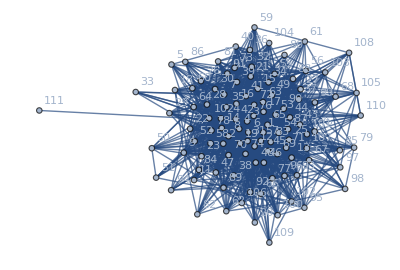

Done With Effective Transition

Done With Spectral Embedding

Done With Shortest Path

Done With Common Neighbors

Done With Preferential Attatchment

Done With Katz

Done With Page Rank

Predictor | Accuracy | Time
Effective Transition | 0.10929 | 6.42188
SpectralEmbedding | 0.123862 | 0.09375
ShortestPath | 0.111389 | 0.390625
CommonNeighbors | 0.0508475 | 0.078125
PreferentialAttatchment | 0. | 0.0625
Katz | 0. | 0.03125
PageRank | 0. | 0.03125

Haggle Data

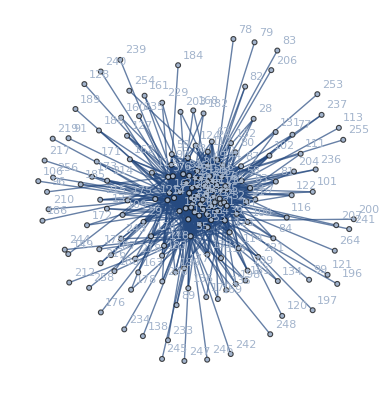

Done With Effective Transition

Done With Spectral Embedding

Done With Shortest Path

Done With Common Neighbors

Done With Preferential Attatchment

Done With Katz

Done With Page Rank

Predictor | Accuracy | Time
Effective Transition | 0. | 35.2656
SpectralEmbedding | 0.086629 | 0.109375
ShortestPath | 0.0377986 | 0.859375
CommonNeighbors | 0.000174004 | 0.46875
PreferentialAttatchment | 0. | 0.453125
Katz | 0. | 0.125
PageRank | 0. | 0.0625

Infectious Data

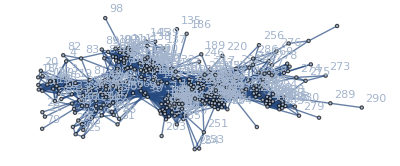

Done With Effective Transition

Done With Spectral Embedding

Done With Shortest Path

Done With Common Neighbors

Done With Preferential Attatchment

Done With Katz

Done With Page Rank

Predictor | Accuracy | Time
Effective Transition | 0.00722543 | 273.063
SpectralEmbedding | 0.00589971 | 0.1875
ShortestPath | 0.0108584 | 3.45313
CommonNeighbors | 0.0015279 | 0.328125
PreferentialAttatchment | 0. | 0.265625
Katz | 0. | 0.140625
PageRank | 0. | 0.140625

```mathematica
files = {{"C:\\Users\\brynbb\\Documents\\Wolfram Mathematica\\hypertextdata.txt","Hyper Text Data"}, {"C:\\Users\\brynbb\\Documents\\Wolfram Mathematica\\haggledata.txt","Haggle Data"},{"C:\\Users\\brynbb\\Documents\\Wolfram Mathematica\\infectiousdata.txt", "Infectious Data"}};

Do[compareScores[file[[1]],file[[2]]], {file,files}]
```